```mathematica
n = 100
```

100

```mathematica
ca = ConstantArray
```

ConstantArray

```mathematica
dm = DiagonalMatrix
```

DiagonalMatrix

```mathematica
A = dm[ca[3,n]] + dm[ca[1, n-1], 1] + dm[ca[1, n-1], -1] + dm[ca[0.2, n-2], 2] + dm[ca[0.2, n-2], -2]
```

{{3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.,0.2},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.,1.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.2,1.,3.}}

```mathematica
b = Array[#&, n]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100}

```mathematica
x = LinearSolve[A, b]
```

{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792}

```mathematica
normaX = Norm[x]
```

109.144

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/wojtek/Dev/metody-numeryczne-fais/num5

```mathematica
gaussX = Import["gauss-seidel.csv", "CSV"]
```

{{0.333333,0.555556,0.792593,1.0321,1.26979,1.50793,1.74604,1.98413,2.22222,2.46032,2.69841,2.93651,3.1746,3.4127,3.65079,3.88889,4.12698,4.36508,4.60317,4.84127,5.07937,5.31746,5.55556,5.79365,6.03175,6.26984,6.50794,6.74603,6.98413,7.22222,7.46032,7.69841,7.93651,8.1746,8.4127,8.65079,8.88889,9.12698,9.36508,9.60317,9.84127,10.0794,10.3175,10.5556,10.7937,11.0317,11.2698,11.5079,11.746,11.9841,12.2222,12.4603,12.6984,12.9365,13.1746,13.4127,13.6508,13.8889,14.127,14.3651,14.6032,14.8413,15.0794,15.3175,15.5556,15.7937,16.0317,16.2698,16.5079,16.746,16.9841,17.2222,17.4603,17.6984,17.9365,18.1746,18.4127,18.6508,18.8889,19.127,19.3651,19.6032,19.8413,20.0794,20.3175,20.5556,20.7937,21.0317,21.2698,21.5079,21.746,21.9841,22.2222,22.4603,22.6984,22.9365,23.1746,23.4127,23.6508,23.8889},{0.0953086,0.301893,0.464329,0.634637,0.80512,0.97503,1.14513,1.31519,1.48526,1.65533,1.8254,1.99546,2.16553,2.3356,2.50567,2.67574,2.8458,3.01587,3.18594,3.35601,3.52608,3.69615,3.86621,4.03628,4.20635,4.37642,4.54649,4.71655,4.88662,5.05669,5.22676,5.39683,5.56689,5.73696,5.90703,6.0771,6.24717,6.41723,6.5873,6.75737,6.92744,7.09751,7.26757,7.43764,7.60771,7.77778,7.94785,8.11791,8.28798,8.45805,8.62812,8.79819,8.96825,9.13832,9.30839,9.47846,9.64853,9.81859,9.98866,10.1587,10.3288,10.4989,10.6689,10.839,11.0091,11.1791,11.3492,11.5193,11.6893,11.8594,12.0295,12.1995,12.3696,12.5397,12.7098,12.8798,13.0499,13.22,13.39,13.5601,13.7302,13.9002,14.0703,14.2404,14.4104,14.5805,14.7506,14.9206,15.0907,15.2608,15.4308,15.6009,15.771,15.941,16.1111,16.2812,16.4512,16.6213,18.3998,26.092},{0.201747,0.402332,0.587219,0.777396,0.967035,1.15644,1.34597,1.53547,1.72498,1.91448,2.10398,2.29349,2.48299,2.6725,2.862,3.05151,3.24101,3.43052,3.62002,3.80952,3.99903,4.18853,4.37804,4.56754,4.75705,4.94655,5.13605,5.32556,5.51506,5.70457,5.89407,6.08358,6.27308,6.46259,6.65209,6.84159,7.0311,7.2206,7.41011,7.59961,7.78912,7.97862,8.16812,8.35763,8.54713,8.73664,8.92614,9.11565,9.30515,9.49466,9.68416,9.87366,10.0632,10.2527,10.4422,10.6317,10.8212,11.0107,11.2002,11.3897,11.5792,11.7687,11.9582,12.1477,12.3372,12.5267,12.7162,12.9057,13.0952,13.2847,13.4742,13.6638,13.8533,14.0428,14.2323,14.4218,14.6113,14.8008,14.9903,15.1798,15.3693,15.5588,15.7483,15.9378,16.1273,16.3168,16.5063,16.6958,16.8853,17.0748,17.2643,17.4538,17.6433,17.8328,18.0224,18.2119,18.2941,17.4818,17.2558,26.4159},{0.160075,0.365742,0.543813,0.728238,0.912455,1.09628,1.28025,1.46421,1.64816,1.83211,2.01606,2.20001,2.38396,2.56791,2.75186,2.93581,3.11976,3.30372,3.48767,3.67162,3.85557,4.03952,4.22347,4.40742,4.59137,4.77533,4.95928,5.14323,5.32718,5.51113,5.69508,5.87903,6.06298,6.24693,6.43089,6.61484,6.79879,6.98274,7.16669,7.35064,7.53459,7.71854,7.90249,8.08645,8.2704,8.45435,8.6383,8.82225,9.0062,9.19015,9.3741,9.55805,9.74201,9.92596,10.1099,10.2939,10.4778,10.6618,10.8457,11.0297,11.2136,11.3976,11.5815,11.7655,11.9494,12.1334,12.3173,12.5013,12.6852,12.8692,13.0531,13.2371,13.421,13.605,13.7889,13.9729,14.1568,14.3408,14.5247,14.7087,14.8926,15.0766,15.2605,15.4445,15.6284,15.8124,15.9963,16.1803,16.3642,16.5482,16.7321,16.9161,17.1001,17.284,17.4751,17.7592,18.271,17.8794,17.0168,26.4691},{0.175165,0.378458,0.558593,0.744668,0.930428,1.11585,1.30141,1.48695,1.67248,1.85802,2.04356,2.2291,2.41464,2.60017,2.78571,2.97125,3.15679,3.34232,3.52786,3.7134,3.89894,4.08448,4.27001,4.45555,4.64109,4.82663,5.01216,5.1977,5.38324,5.56878,5.75432,5.93985,6.12539,6.31093,6.49647,6.682,6.86754,7.05308,7.23862,7.42416,7.60969,7.79523,7.98077,8.16631,8.35184,8.53738,8.72292,8.90846,9.094,9.27953,9.46507,9.65061,9.83615,10.0217,10.2072,10.3928,10.5783,10.7638,10.9494,11.1349,11.3204,11.506,11.6915,11.8771,12.0626,12.2481,12.4337,12.6192,12.8048,12.9903,13.1758,13.3614,13.5469,13.7324,13.918,14.1035,14.2891,14.4746,14.6601,14.8457,15.0312,15.2167,15.4023,15.5878,15.7734,15.9589,16.1444,16.33,16.5155,16.701,16.8866,17.0721,17.2572,17.4338,17.5671,17.6998,18.168,17.9938,16.9678,26.4778},{0.169941,0.374177,0.553694,0.739291,0.924614,1.10958,1.29469,1.47977,1.66485,1.84994,2.03502,2.22011,2.40519,2.59028,2.77536,2.96044,3.14553,3.33061,3.5157,3.70078,3.88587,4.07095,4.25604,4.44112,4.6262,4.81129,4.99637,5.18146,5.36654,5.55163,5.73671,5.9218,6.10688,6.29196,6.47705,6.66213,6.84722,7.0323,7.21739,7.40247,7.58756,7.77264,7.95772,8.14281,8.32789,8.51298,8.69806,8.88315,9.06823,9.25332,9.4384,9.62348,9.80857,9.99365,10.1787,10.3638,10.5489,10.734,10.9191,11.1042,11.2892,11.4743,11.6594,11.8445,12.0296,12.2147,12.3998,12.5848,12.7699,12.955,13.1401,13.3252,13.5103,13.6953,13.8804,14.0655,14.2506,14.4357,14.6208,14.8058,14.9909,15.176,15.3611,15.5462,15.7313,15.9164,16.1014,16.2865,16.4716,16.6567,16.8418,17.0276,17.2189,17.4228,17.6,17.7162,18.1255,18.0226,16.9582,26.4791},{0.171695,0.375585,0.555288,0.741022,0.926469,1.11156,1.2968,1.48202,1.66723,1.85244,2.03766,2.22287,2.40808,2.5933,2.77851,2.96373,3.14894,3.33415,3.51937,3.70458,3.8898,4.07501,4.26022,4.44544,4.63065,4.81587,5.00108,5.18629,5.37151,5.55672,5.74194,5.92715,6.11236,6.29758,6.48279,6.66801,6.85322,7.03843,7.22365,7.40886,7.59407,7.77929,7.9645,8.14972,8.33493,8.52014,8.70536,8.89057,9.07579,9.261,9.44621,9.63143,9.81664,10.0019,10.1871,10.3723,10.5575,10.7427,10.9279,11.1131,11.2984,11.4836,11.6688,11.854,12.0392,12.2244,12.4096,12.5949,12.7801,12.9653,13.1505,13.3357,13.5209,13.7061,13.8913,14.0766,14.2618,14.447,14.6322,14.8174,15.0026,15.1878,15.3731,15.5583,15.7435,15.9287,16.1139,16.2991,16.4843,16.6695,16.8541,17.0362,17.2167,17.4109,17.6015,17.7288,18.1122,18.0293,16.9564,26.4793},{0.171119,0.37513,0.554777,0.740472,0.925883,1.11094,1.29614,1.48132,1.66649,1.85167,2.03685,2.22202,2.4072,2.59238,2.77756,2.96273,3.14791,3.33309,3.51826,3.70344,3.88862,4.07379,4.25897,4.44415,4.62933,4.8145,4.99968,5.18486,5.37003,5.55521,5.74039,5.92556,6.11074,6.29592,6.48109,6.66627,6.85145,7.03663,7.2218,7.40698,7.59216,7.77733,7.96251,8.14769,8.33286,8.51804,8.70322,8.8884,9.07357,9.25875,9.44393,9.6291,9.81428,9.99946,10.1846,10.3698,10.555,10.7402,10.9253,11.1105,11.2957,11.4809,11.666,11.8512,12.0364,12.2216,12.4068,12.5919,12.7771,12.9623,13.1475,13.3326,13.5178,13.703,13.8882,14.0734,14.2585,14.4437,14.6289,14.8141,14.9992,15.1844,15.3696,15.5548,15.7399,15.9251,16.1103,16.2955,16.4807,16.6663,16.8527,17.0384,17.22,17.4084,17.5988,17.7338,18.1086,18.0308,16.9561,26.4793},{0.171305,0.375275,0.554939,0.740645,0.926067,1.11113,1.29635,1.48153,1.66672,1.85191,2.03709,2.22228,2.40747,2.59266,2.77784,2.96303,3.14822,3.33341,3.51859,3.70378,3.88897,4.07416,4.25935,4.44453,4.62972,4.81491,5.0001,5.18528,5.37047,5.55566,5.74085,5.92603,6.11122,6.29641,6.4816,6.66678,6.85197,7.03716,7.22235,7.40753,7.59272,7.77791,7.9631,8.14828,8.33347,8.51866,8.70385,8.88903,9.07422,9.25941,9.4446,9.62978,9.81497,10.0002,10.1853,10.3705,10.5557,10.7409,10.9261,11.1113,11.2965,11.4817,11.6668,11.852,12.0372,12.2224,12.4076,12.5928,12.778,12.9632,13.1483,13.3335,13.5187,13.7039,13.8891,14.0743,14.2595,14.4447,14.6298,14.815,15.0002,15.1854,15.3706,15.5558,15.741,15.9262,16.1113,16.2965,16.4815,16.6663,16.8517,17.0378,17.2212,17.4085,17.5972,17.7354,18.1077,18.0311,16.956,26.4792},{0.171246,0.375229,0.554888,0.740591,0.92601,1.11107,1.29628,1.48147,1.66665,1.85184,2.03702,2.2222,2.40739,2.59257,2.77776,2.96294,3.14813,3.33331,3.5185,3.70368,3.88886,4.07405,4.25923,4.44442,4.6296,4.81479,4.99997,5.18516,5.37034,5.55553,5.74071,5.92589,6.11108,6.29626,6.48145,6.66663,6.85182,7.037,7.22219,7.40737,7.59255,7.77774,7.96292,8.14811,8.33329,8.51848,8.70366,8.88885,9.07403,9.25922,9.4444,9.62958,9.81477,9.99995,10.1851,10.3703,10.5555,10.7407,10.9259,11.1111,11.2962,11.4814,11.6666,11.8518,12.037,12.2222,12.4074,12.5925,12.7777,12.9629,13.1481,13.3333,13.5185,13.7036,13.8888,14.074,14.2592,14.4444,14.6296,14.8148,14.9999,15.1851,15.3703,15.5555,15.7407,15.9259,16.1111,16.2963,16.4816,16.6666,16.8517,17.0374,17.2214,17.4089,17.5966,17.7359,18.1075,18.0311,16.956,26.4792},{0.171265,0.375243,0.554904,0.740608,0.926027,1.11109,1.2963,1.48149,1.66667,1.85186,2.03704,2.22223,2.40741,2.5926,2.77778,2.96297,3.14815,3.33334,3.51853,3.70371,3.8889,4.07408,4.25927,4.44445,4.62964,4.81482,5.00001,5.18519,5.37038,5.55556,5.74075,5.92594,6.11112,6.29631,6.48149,6.66668,6.85186,7.03705,7.22223,7.40742,7.5926,7.77779,7.96297,8.14816,8.33335,8.51853,8.70372,8.8889,9.07409,9.25927,9.44446,9.62964,9.81483,10.,10.1852,10.3704,10.5556,10.7408,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.0371,12.2222,12.4074,12.5926,12.7778,12.963,13.1482,13.3334,13.5185,13.7037,13.8889,14.0741,14.2593,14.4445,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7408,15.9259,16.1111,16.2963,16.4815,16.6667,16.8518,17.0372,17.2214,17.4091,17.5964,17.736,18.1074,18.0312,16.956,26.4792},{0.171259,0.375239,0.554899,0.740603,0.926022,1.11109,1.2963,1.48148,1.66666,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18518,5.37037,5.55555,5.74074,5.92592,6.11111,6.29629,6.48148,6.66666,6.85185,7.03703,7.22222,7.4074,7.59259,7.77777,7.96296,8.14814,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8518,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8518,17.0372,17.2213,17.4092,17.5963,17.736,18.1074,18.0312,16.956,26.4792},{0.171261,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44445,4.62963,4.81482,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07408,9.25926,9.44445,9.62963,9.81482,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18518,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5.,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10.,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792},{0.17126,0.37524,0.5549,0.740604,0.926023,1.11109,1.2963,1.48148,1.66667,1.85185,2.03704,2.22222,2.40741,2.59259,2.77778,2.96296,3.14815,3.33333,3.51852,3.7037,3.88889,4.07407,4.25926,4.44444,4.62963,4.81481,5,5.18519,5.37037,5.55556,5.74074,5.92593,6.11111,6.2963,6.48148,6.66667,6.85185,7.03704,7.22222,7.40741,7.59259,7.77778,7.96296,8.14815,8.33333,8.51852,8.7037,8.88889,9.07407,9.25926,9.44444,9.62963,9.81481,10,10.1852,10.3704,10.5556,10.7407,10.9259,11.1111,11.2963,11.4815,11.6667,11.8519,12.037,12.2222,12.4074,12.5926,12.7778,12.963,13.1481,13.3333,13.5185,13.7037,13.8889,14.0741,14.2593,14.4444,14.6296,14.8148,15.,15.1852,15.3704,15.5556,15.7407,15.9259,16.1111,16.2963,16.4815,16.6667,16.8519,17.0372,17.2213,17.4092,17.5963,17.7361,18.1074,18.0312,16.956,26.4792}}

```mathematica
jacobiX = Import["jacobi.csv", "CSV"]
```

{1}
 |  |  |  |

```mathematica
deltaJacobi[iter_]:=Abs[Norm[jacobiX[[iter]]] - normaX]
```

```mathematica
deltaGauss[iter_]:=Abs[Norm[gaussX[[iter]]]-normaX]
```

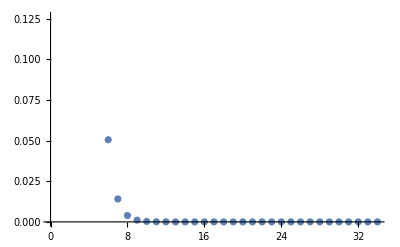

```mathematica
ListPlot[Array[deltaGauss, Length[gaussX]]]
```

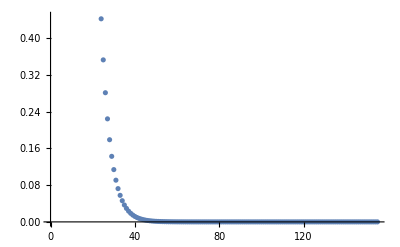

```mathematica
ListPlot[Array[deltaJacobi, Length[jacobiX]]]
```

```mathematica
Export["przyblizenia-gauss.csv", Array[deltaGauss, Length[gaussX]]]
```

przyblizenia-gauss.csv

```mathematica
Export["przyblizenia-jacobi.csv", Array[deltaJacobi, Length[jacobiX]]]
```

przyblizenia-jacobi.csv